```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

## Useful Functions

Some of Georgs most used Mathematica function

### File loading

Returns all the filenames with a given pattern in the given directory.
Very useful to select the right log file, or e.g. process all logfile.

```mathematica
GetFiles[dir_String,pattern_] :=
Module[{pwd,fs},
pwd= Directory[];
SetDirectory[dir];
fs= FileNames[pattern];
SetDirectory[pwd];
 Map[dir<># & , fs]
]
```

### Plotting

Calculates size of image (to use with ImageSize ->) based on Pagefraction

```mathematica
CalcImgSize[pagefraction_]:=460pagefraction;
```

```mathematica
(*creates m colors from "indexed" schemes n *)
Colors[n_Integer,m_Integer]:=Table[ColorData[n][x],{x,1,m}]
```

```mathematica
ColorsFromScheme[n_Integer,scheme_String]:=Table[ColorData[scheme][x],{x,0,1,1/(n-1)}]
```

Set the font style in Plot and ListPlot3D (add ListLinePlot and the like if required)

```mathematica
SetOptions[Plot,LabelStyle->Directive[FontFamily->Times,FontSize->10],PlotStyle->Thick,PlotTheme->None];
SetOptions[ListPlot3D,LabelStyle->Directive[FontFamily->Times,FontSize->10],PlotTheme->None];
```

SetOptions::optnf: PlotTheme is not a known option for Plot.

SetOptions::optnf: PlotTheme is not a known option for ListPlot3D.

```mathematica
SetOptions[ListLogLinearPlot,LabelStyle->Directive[FontFamily->Times,FontSize->10],PlotTheme->None];
```

SetOptions::optnf: PlotTheme is not a known option for ListLogLinearPlot.

### LinePlotting that uses third dimension for coloring

```mathematica
Options[ListLinePlot2p5D]=Options[ListLinePlot];
```

```mathematica
ListLinePlot2p5D[dat_,opts:OptionsPattern[ListLinePlot2p5D]]:=Module[{range,colorscaling,colors,coloring,opts4plot},
range={Min[dat[[All,3]]],Max[dat[[All,3]]]};
colorscaling=RescalingTransform[{range}];
colors=OptionValue[ColorFunction]/.{Automatic->ColorData["Rainbow"]};
coloring[x_]=colors[First[colorscaling[{x}]]];
opts4plot = FilterRules[{opts},Options[Graphics]];
Graphics[Flatten[{OptionValue[PlotStyle]/.Automatic->{},Map[Line[#[[All,{1,2}]],VertexColors->coloring/@#[[All,3]]]&,Partition[dat,2,1]]}],Axes->True,AspectRatio->1/GoldenRatio,opts4plot]
]
```

### Data Manipulation

Very useful functions to zip lists. 
   e.g. Zip [{1, 2}, {3, 4}] -> {{1, 3}, {2, 4}}

```mathematica
Zip[l1_List,l2_List]:=Thread[List[l1,l2]]
Zip3[l1_List,l2_List,l3_List]:=Thread[List[l1,l2,l3]]
Zip4[l1_List,l2_List,l3_List, l4_List]:=Thread[List[l1,l2,l3,l4]]
(*ZipS but uses shortest common list*)
ZipS[l1_List,l2_List]:=Module[{mlen},
mlen=Min[Length[l1],Length[l2]];
Thread[List[Take[l1,mlen],Take[l2,mlen]]]]
```

Gives you every xth element, but as an average over the skipped interval. Or better it gived the average of partitions of size x.

```mathematica
EveryXAvg[data_List, x_Integer] := Module[{parts},
parts = Partition[data,x];
Map[ReplacePart[#,0->Plus]/x&,parts]
]
```

```mathematica
EveryXFun[data_List, x_Integer,fun_] := Module[{parts},
parts = Partition[data,x];
Map[fun[#]&,parts]
]
```

This gives you the index of the center element of the partitioning in the above functions.

```mathematica
EveryXIndex[data_List, x_Integer] := Module[{},
Table[x,{x,x/2,Length[data],x}]
]
```

Calculates an average over x subsequent values, the averaging window is shifted by n

```mathematica
EveryXAvgSliding[data_List, x_Integer,n_Integer] := Module[{parts},
parts = Partition[data,x,n];
Map[ReplacePart[#,0->Plus]/x&,parts]
]
```

applies function to nth element of list

```mathematica
MapNth[f_,x_,n_]:= ReplacePart[x, n ->f[ x[[n]] ]]
```

maps the second coordinate of a time series

```mathematica
MapTimeSeries[fun_, dat_]:=Map[MapNth[fun,#,2]&,dat];
```

replaces a potentially missing result by a default value

```mathematica
DefaultMissing[maybeMissing_,default_]:=If[maybeMissing[[0]]===Missing,default,maybeMissing];
```

sum and product of a list

```mathematica
SumList[m_]:=ReplacePart[Flatten[m],0->Plus];
ProdList[m_]:=ReplacePart[Flatten[m],0->Times];
```

return {max, index} of the maximal element of the list

```mathematica
MaxWithPosition[list_]:=Block[{m=Max[list]},{m,First[FirstPosition[list,m]]}];
```

From a data series {{x, y}, ...}, select those where x is within given range (also removes non-numbers)

```mathematica
SelectRange[dat_,range_]:=Module[{int},int=Interval[range];
Select[dat,IntervalMemberQ[int,#[[1]]]&&(And@@NumberQ/@#)&]];
```

## Tisean Plotting Routines - Calculate Entropies and Excess Entropy from TISEAN d2

What is in the tisean files output by d2?
The h2 files contain the entropy rate

h (m, ϵ) = H (m + 1, ϵ) - H (m, ϵ)

where H (m, ϵ) = - ln C (m, ϵ)  is the Block Entropy of dimension m with resolution ϵ. However these are Renyi type entropies.
C is the correlation integral (c2).
d2 contains the log-log derivative of C

```mathematica
StyleLabel[x_,size_:10]:=Style[x ,size,Bold,FontFamily->"Times New Roman"];
StyleAxisLabel[x_,size_:12]:=Style[x ,size,FontFamily->"Times New Roman"];
```

```mathematica
RoundNumbersInExp[exp_,val_: 0.01]:=exp/.{t:_?NumberQ:>Round[t,val]};
```

```mathematica
Eps=StyleAxisLabel[ϵ];
EEm=StyleAxisLabel["E_m^(2)"];
PIm=StyleAxisLabel["PI_m"];
D2m=StyleAxisLabel["D_m^(2)"];
h2m=StyleAxisLabel["h_m^(2)"];
H2m=StyleAxisLabel["H_m^(2)"];
CCm=StyleAxisLabel["Cc_m^(2)"];
```

```mathematica
LoadTiseanFile[file_String,print_: False]:=
Module[{dat,series,blocks},
dat = Import[file,"Table"];
blocks = DeleteCases[Split[dat,And[#1≠{},#2≠{}]&],{{}}];
series =Map[DeleteCases[#,Except[{_Real,_Real}]]&,blocks];
If[print==True,Print[ dat[[1]]]];
If[print==True,Print["Read " <>ToString[Length[series]]<> " blocks with "
	<> ToString[Length[series[[1]]]]<>" datasets"]];
series
]
```

```mathematica
(*This function does not make sense because the data in each column does not have the same length *)
MergeTisean[dat_]:=Module[{firstcol},
firstcol=dat[[All,All,1]];
Assert[And @@Map[First[firstcol] == #&,firstcol],"The first column must be identical" ];
{dat[[1,All,1]]} ~Join~dat[[All,All,2]]
]
```

```mathematica
LoadTiseanLyapFile[file_String,print_: False]:=
Module[{dat,series},
dat = Import[file,"Table"];
series =dat; (*Map[DeleteCases[#,Except[{_Integer,___}]]&,dat];*)
If[print==True,Print[ dat[[1]]]];
If[print==True,Print["Read " <>ToString[Length[series]]<> " with "
	<> ToString[Length[series[[1]]]]<>" columns"]];
series
]
```

```mathematica
ChangeExtension[name_,ending_]:=StringReplace[name,RegularExpression["\\.[^.]*$"]->ending]
```

```mathematica
ZipWith[f_Function,l1_List,l2_List]:=Map[f @@ #&,ZipS[l1,l2]];
```

Substract two series (e.g. lines in the h2 plot)

```mathematica
DiffSeries[pair_]:=ZipWith[Function[{a,b},{a[[1]],b[[2]]-a[[2]]}],pair[[1]],pair[[2]]]
```

```mathematica
LogDerivativeSeries[xylists_,k_]:=Module[{n},
n=Max[k,3];
n=If[EvenQ[n],n+1,n];
Map[Function[{x,l},{x,Mean[Map[(#[[2,2]]-#[[1,2]])/(Log[#[[2,1]]]-Log[#[[1,1]]])&,Partition[l,2,1]]]}]@@#&,Zip[xylists[[All,1]],Partition[xylists,n,1,{-Round[(n+1)/2],Round[(n+1)/2]},{}]]]
]
```

```mathematica
ExcessEntropySum[deltaHs_,n_Integer,i_Integer]:=Module[{ls},
{deltaHs[[1,i,1]],
If[And@@Map[Length[#]≥i&,deltaHs[[1;;n]]],
Sum[k deltaHs[[k,i,2]],{k,1,n}],
Undefined
]}
]
```

```mathematica
ExcessEntropies[deltaHs_]:=Table[Table[ExcessEntropySum[deltaHs,n,i],{i,1,Length[deltaHs[[1]]]}],{n,1,Length[deltaHs]}];
```

```mathematica
DiffDimSchreiber[Ds_,d_]:=Table[Table[{Ds[[m,i,1]],(Ds[[m,i,2]]-Ds[[d,i,2]])/(m-d)},{i,1,Min[Length[Ds[[m]]],Length[Ds[[d]]]]}],{m,d+1,Length[Ds]}];
```

```mathematica
DerivativeDiffPast2[l_List]:=(#[[2]]-#[[1]])&/@Partition[Prepend[l,l[[1]]],2,1]
```

```mathematica
CutWhenWigly[list_List,thresh_]:=Module[{diff2},diff2=DerivativeDiffPast2[DerivativeDiffPast2[list[[All,2]]]];
TakeWhile[Zip[diff2,list],Abs[#[[1]]]<thresh&][[All,2]]]
```

Extracts data from tisean output, calculates Excess Entropy etc and generates plots.

```mathematica
Options[TiseanD2PlotsAndData]={ColorPalette->"Rainbow",EpsRange->All,Thresh->Infinity, ShowEntropy->False,ShowCSum->False,CleanDeltaH->False}~Join~Options[ListLogLinearPlot]; 
ColorPalette::usage="Palette to be used (default:Rainbow)";
Thresh::usage="maximum of 2nd derivative, before it is but";
ShowEntropy::usage="Show plot for block entropies";
ShowCSum::usage="Show plot for correlation sum";
CleanDeltaH::usage="Fit the wigling parts of deltaH";
EpsRange::usage="Restrict epsilon range";
```

```mathematica
TiseanD2PlotsAndData::usage="Extracts data from tisean output, calculates Excess Entropy etc and generates plots. Returns {plots,data}.
Provide any of the tisean output files (e.g. the .d2) and the spatial embedding dimension (d in the paper)";
```

```mathematica
SelectRange[dat_,range_]:=Module[{int},int=Interval[range];
Select[dat,IntervalMemberQ[int,#[[1]]]&&(And@@NumberQ/@#)&]];
```

```mathematica
TiseanD2PlotsAndData[filename_,dim_,opts:OptionsPattern[TiseanD2PlotsAndData]]:=Module[{files,epsRange,d2,h2,c2,indices,H,h,deltaH,deltaHorig,en,den,len,core, core2, opts4plot,thresh,colors,data},
files=Map[ChangeExtension[filename,#]&,{".d2",".h2",".c2"}];
epsRange=OptionValue[EpsRange];
d2=LoadTiseanFile[files[[1]],True];
h2=LoadTiseanFile[files[[2]],False];
c2=LoadTiseanFile[files[[3]],False];
If[Not[epsRange===All],
d2=SelectRange[#,epsRange]&/@d2;h2=SelectRange[#,epsRange]&/@h2;c2=SelectRange[#,epsRange]&/@c2;
];
len=Length[d2];
indices=Table[(x)*dim,{x,1,Length[c2]/dim}];
H=Map[Map[{#[[1]],-Log[#[[2]]]}&,#]&,c2[[indices]]];
h=Prepend[Map[DiffSeries,Partition[H,2,1]],H[[1]]];
deltaHorig=Map[DiffSeries,Reverse /@Partition[h,2,1]];
deltaH=If[OptionValue[CleanDeltaH],Map[FitEndOfRange[#,Max[0,#]&]&,deltaHorig], deltaHorig];
en=Table[n H[[n-1]] - (n-1) H[[n]],{n,2,Length[H]}];
(* en=ExcessEntropies[deltaH]; *) (* The same as above*)
den=Map[Map[MapNth[-#&,#,2]&,LogDerivativeSeries[#,5]]&,en];
thresh = OptionValue[Thresh];
opts4plot = FilterRules[{opts},Options[ListLogLinearPlot]];
colors=ColorsFromScheme[len,OptionValue[ColorPalette]];
data={"D"->d2,"h"->h,"E"->en,"DE"->den,"deltaH"->deltaH,"H"->H};
{{ListLogLinearPlot[CutWhenWigly[#,thresh]&/@d2, opts4plot, Joined->True,ImageSize->350,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->files[[1]] ,PlotStyle->colors,AxesLabel->{Eps,D2m}],
If[Length[h]>0,ListLogLinearPlot[CutWhenWigly[#,thresh]&/@h, opts4plot,Joined->True,ImageSize->350,PlotLabel->"entropy rate " ,AxesLabel->{Eps,h2m},PlotStyle->Prepend[colors,Darker[Gray]]],Null],
If[Length[en]>0,ListLogLinearPlot[CutWhenWigly[#,thresh]&/@en, opts4plot,Joined->True,PlotRange->All,
ImageSize->350,PlotLabel->"excess entropy",AxesLabel->{Eps,EEm},PlotStyle->Drop[colors,1]],Null],
If[Length[den]>0,ListLogLinearPlot[CutWhenWigly[#,thresh]&/@den, opts4plot,Joined->True,PlotRange->{All,{0,Automatic}},ImageSize->350,
GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],
PlotLabel->"Dim of excess entropy",PlotStyle->colors],Null],
If[Length[deltaH]>0,ListLogLinearPlot[deltaH, opts4plot,Joined->True,PlotRange->All,ImageSize->350,PlotLabel->"δh_m^(2)",PlotStyle->colors,AxesLabel->{Eps,"δh_m^(2)"}],Null],
If[OptionValue[ShowCSum],
If[Length[c2]>0,ListLogLinearPlot[c2, opts4plot,Joined->True,PlotRange->All,ImageSize->350,PlotLabel->"c_m^(2)",PlotStyle->colors],Null],
If[Length[deltaH]>0 && OptionValue[CleanDeltaH],ListLogLinearPlot[deltaHorig, opts4plot,Joined->True,PlotRange->All,ImageSize->350,PlotLabel->"δh_m^(2)- original",PlotStyle->colors],Null]
],
If[Length[H]>0 && OptionValue[ShowEntropy],ListLogLinearPlot[H, opts4plot,Joined->True,PlotRange->All,ImageSize->350,PlotLabel->"Entropies",AxesLabel->{Eps,H2m},PlotStyle->colors],Null]
},
data}
]
```

This function tries to fit logarithmic curve at the end of the data range (small scales) It automatically figures out the right range, but only uses 30 datapoints from the end of the data (ignoring the Indeterminate). The remainder (below the fitting range) of the series is replaces by the fit that is additionally passed though func (id by default).

```mathematica
FitEndOfRange[dat_,func_:Identity]:=Module[{end,pos,fit,rangestart,model},
pos=First[FirstPosition[dat,_?((Not[NumberQ[#[[2]]]])&),{Length[dat]},{1},Heads->False]];
end=First[dat[[Max[1,pos-30]]]];
fit=NonLinearFitWithAutoCutOff[dat,c111-d111 Log[x],{c111,d111},x,0.0001,{0.0,end}];
rangestart=fit[[2,1]];
model=fit[[1]];
Map[If[#[[1]]<=rangestart,{#[[1]],func[model[#[[1]]]]},#]&,dat]
]
```

```mathematica
TiseanPlotDiffDim[filename_,fromdim_,todim_,opts:OptionsPattern[TiseanPlotAllMultiDim]]:=Module[{files,d2,diffDs,len, opts4plot,thresh,colors},
files=Map[ChangeExtension[filename,#]&,{".d2",".h2",".c2"}];
d2=LoadTiseanFile[files[[1]],True];len=Length[d2];
diffDs=Table[{d,DiffDimSchreiber[d2,d]},{d,fromdim,todim}];
test=diffDs;
thresh = OptionValue[Thresh];
opts4plot = FilterRules[{opts},Options[ListLogLinearPlot]];
colors=ColorsFromScheme[len,OptionValue[ColorPalette]];
Prepend[
Map[ListLogLinearPlot[#[[2]], opts4plot, Joined->True,ImageSize->350,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->files[[1]] ,PlotStyle->Drop[colors,#[[1]]],AxesLabel->{Eps,(Subscript[D, m]-Subscript[D, #[[1]]])/(m-#[[1]])}]&,
diffDs],
ListLogLinearPlot[CutWhenWigly[#,thresh]&/@d2, opts4plot, Joined->True,ImageSize->350,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed],PlotLabel->files[[1]] ,PlotStyle->colors,AxesLabel->{Eps,D2m}]]
]
```

#### Legend

```mathematica
Needs["PlotLegends`"]
```

```mathematica
TiseanLegend[num_Integer,with0_:True,scheme_String:"Rainbow"]:=Module[{colors},
colors=ColorsFromScheme[num,scheme];
If[with0,PrependTo[colors,Darker[Gray]]];
Graphics[Legend[MapIndexed[{Graphics[{#1,Thick, Line[{{0,0},{1,0}}]}],If[Mod[#2[[1]],2]==1,If[with0,#2[[1]]-1,#2[[1]]],""]}&,colors],LegendLabel->m,LegendTextSpace->1.5, LegendSpacing->0,LegendShadow->None,LegendBackground->Opacity[0],LegendLabelSpace->2,LegendBorder->None,ShadowBackground ->Opacity[0]],ImageSize->20]
]
```

```mathematica
TiseanLegendNew[num_Integer,with0_:True,scheme_String:"Rainbow"]:=Module[{colors},
colors=ColorsFromScheme[num,scheme];
If[with0,PrependTo[colors,Darker[Gray]]];LineLegend[colors,MapIndexed[If[Mod[#2[[1]],2]==1,If[with0,#2[[1]]-1,#2[[1]]],""]&,colors],LegendLabel->m,LegendLayout->{"Column",1}]]
```

#### test

```mathematica
LogDerivativeSeries[Table[{Exp[x],x^2},{x,1,6}],3]
```

{{ⅇ,3},{ⅇ^2,4},{ⅇ^3,6},{ⅇ^4,8},{ⅇ^5,10},{ⅇ^6,11}}

## Fitting - Function to perform Fitting with automated range detection

```mathematica
LogLinFitFun=NonlinearModelFit[#,c-d Log[x],{c,d},x]&;
ConstFitFun=LinearModelFit[#,0,x]&;
```

### Fully Automatic Fitting rountines for many segment fitting

Combined fitting function : First determines threshold for quality of fits from all fits of minimal size. Use given quantile + 0.1σ  of fits quality for threshold.
Then get the longest fits for all good positions and select the largest among them (30% overlap allowed)

```mathematica
(*FitQualityCriterion[model_]:=Variance[model["FitResiduals"]];*)
(*FitQualityCriterion[model_]:=model["EstimatedVariance"];*)
FitQualityCriterion[model_]:=Total[model["FitResiduals"]^2];
(*FitQualityCriterion[model_]:=Mean[model["FitResiduals"]]+StandardDeviation[model["FitResiduals"]];*)
(*FitQualityCriterion[model_]:=Max[ReplacePart[model["ParameterConfidenceIntervals"],{{1,0},{2,0}}->Subtract]];*)

FindAllFits[data_,fitfun_,minPoints_,quantile_:0.25]:=Module[{cleaned,shortfits,fiterrors,thresh,goodintervals},
(*joined = SortBy[Select[If[Head[data[[1,1]]]===List,Flatten[data,1],data],(And@@NumberQ/@#)&],First];*)
cleaned=Select[data,(And@@NumberQ/@#)&];
shortfits=FitShortRegions[cleaned,fitfun,minPoints];
     fiterrors=Map[FitQualityCriterion, shortfits[[All,1]]];
thresh=Quantile[fiterrors,quantile]+0.1StandardDeviation[fiterrors];
goodintervals=Select[Zip[shortfits,fiterrors],#[[2]]<thresh&][[All,1,2]];
SelectInvervals[Select[Map[FindMaxFitRegion[cleaned,fitfun,2*thresh,#,minPoints]&,goodintervals[[All,1]]],Length[#]>0&]]
]
```

Returns fits on all regions of given size

```mathematica
FitShortRegions[data_,fitfun_,size_:10]:=Module[{len,low,up,fits,range,fitter,criterion},
len=Length[data];
(*first check upwards*)
fitter=Function[{range},
fitfun[data[[range[[1]];;range[[2]]]]] 
];
fits=Map[{fitter[#],#}&,Table[{i,i+size},{i,1,len-size,1}]]
(*fits=Map[fitter,Flatten[Table[{i,j},{i,1,len-size,1},{j,i+size,len,1}],1]]*)
]
```

starting from a certain point, try to increase Region where a good fit can be optained. Assumes that data is collated and does not contain Indeterminate etc

```mathematica
FindMaxFitRegion[data_,fitfun_,maxVariance_,index_,minPoints_:6,bothsides_:False]:=Module[{len,low,up,fits,range,fitter,criterion},
len=Length[data];
low=Max[index,1];
up=Min[index+minPoints ,len];
(*first check upwards*)
fitter=Function[{range},
{fitfun[data[[range[[1]];;range[[2]]]]],range} 
];
criterion=Function[{fit},FitQualityCriterion[First[fit]]< maxVariance];
fits=MapWhile[fitter,criterion,Table[{low,i},{i,up,len,1}]];
If[Length[fits]==0,{},
range=Last[fits][[2]];
If[bothsides,
up=range[[2]];
fits=MapWhile[fitter,criterion,Table[{i,up},{i,low,1,-1}]];
If[Length[fits]==0,{},
range=Last[fits][[2]];
{Last[fits][[1]],Sort[data[[range,1]]],range}
]
,{Last[fits][[1]],Sort[data[[range,1]]],range}
]
]
]
```

Maps until a criterium is met (like in Haskell: takeWhile crit $ map fun list)

```mathematica
MapWhile[fun_,crit_,list_List]:=Module[{result, pred,n,len,next},
len=Length[list];
pred=True;
result={};
n=1;
While[pred && n≤len,
next=fun[list[[n]]];
pred=crit[next];
If[pred,AppendTo[result,next]];
n++;
];
result
]
```

```mathematica
MapWhile[#^2&,#<36&,{}]
MapWhile[#^2&,#<36&,{1,2}]
MapWhile[#^2&,#<36&,{1,2,3,4,5,6}]
```

{}

{1,4}

{1,4,9,16,25}

Selection routine for Intervals. For two intervals overlapping more than 30% (w.r.t. smaller), delete smaller one.

```mathematica
IntervalLen[Interval[]]:=0;
IntervalLen[in_Interval]:=Max[in]-Min[in];
IntervalEmpty[in_Interval]:=((in)===(Interval[]));
SelectInvervals[fits_]:=Module[{withInt,n},
withInt=Map[MapNth[Interval,#,3]&,fits];
n=1;
While[n<Length[withInt],
If[IntervalLen[IntervalIntersection[withInt[[n,3]],withInt[[n+1,3]]]]/(Min[IntervalLen[withInt[[n,3]]],IntervalLen[withInt[[n+1,3]]]])<0.3,
n++,
withInt = If[IntervalLen[withInt[[n,3]]]<IntervalLen[withInt[[n+1,3]]],Delete[withInt,n],Delete[withInt,n+1]];
];
];
withInt
]
```

### Merge fits and Data

Replaces fitted intervals in data and tags each point whether it came from an fitted interval.
{{{x,y},True/False},...}

```mathematica
IntervalAndDataTagged[dat_,fits_]:=
Module[{intervals,tagged},
intervals=fits[[All,3]];
tagged=Map[Function[{idx},{idx,Flatten[Position[Map[IntervalMemberQ[#,idx]&,intervals],True]]}],Range[1,Length[dat]]];

Map[Function[{idx,matches},If[Length[matches]<1,{dat[[idx]],0},{{dat[[idx,1]],Mean[Map[#[[1]][dat[[idx,1]]]&,fits[[matches]]]]},1}]]@@#&,tagged]
]
```

### Fitting Routine that enhances fit range automatically (old, see FindAllFits)

```mathematica
If[Length[MaximalBy]==0,
MaximalBy[{},f_]:={};
MaximalBy[exp_,f_]:=Block[{m=Map[f,exp]},exp[[Position[m,Max[m]][[1]]]]]];
```

They can be used to find a fit in a certain interval where both sides of the interval are potentially moved inwards to satisfy quality criterion

```mathematica
GetLongestSubsequence[list_,crit_]:=MaximalBy[Table[{x+1,LengthWhile[Drop[list,x],crit]},{x,0,Length[list]-1}],Last];
```

```mathematica
FitWithAutoCutOff[data_,fitfun_,maxVariance_,initRange_: Null]:=Module[{joined,lm,range,resid,varparams,var,ri,newdat,n},range=initRange;
joined = SortBy[If[Head[data[[1,1]]]===List,Flatten[data,1],data],First];
range=If[initRange===Null,range={Min[joined[[All,1]]],Max[joined[[All,1]]]},initRange];
newdat=SelectRange[joined,range];
lm=fitfun [newdat];
varparams=lm["EstimatedVariance"];
n=1;
While[varparams>maxVariance&&n<20,
(*Print[{range,lm["EstimatedVariance"]}];*)
resid=lm["StudentizedResiduals"];
var=1.5StandardDeviation[resid];
ri=First[GetLongestSubsequence[resid,(Abs[#]≤var&)]];
range=Sort[newdat[[{ri[[1]],ri[[1]]+ri[[2]]-1},1]]];
newdat=SelectRange[newdat,range];
lm=fitfun [newdat];
varparams=lm["EstimatedVariance"];
n++;];
{lm,range,n}]
```

Compatibility

```mathematica
NonLinearFitWithAutoCutOff[data_,form_,params_,vars_,maxVariance_,initRange_:Null]:=
Module[{fitfun},
fitfun=NonlinearModelFit[#,form,params,vars]&;
FitWithAutoCutOff[data,fitfun,maxVariance,initRange]
]
LinearFitWithAutoCutOff[data_,form_,vars_,maxVariance_,initRange_:Null]:=
Module[{fitfun},
fitfun=LinearModelFit[#,form,vars]&;
FitWithAutoCutOff[data,fitfun,maxVariance,initRange]
]
```

### Utility to plot fits and label them

```mathematica
fittedLineStyle=Directive[Black,Opacity[.3],Dotted,AbsoluteThickness[.5]];
```

```mathematica
Options[PlotFitInLog]={ShowLabel->True,LabelSize->10,LabelAngle->0, BasePlotRatio->1,LimiterSize->Tiny,ExtendFit->1, LabelPosition->{Automatic,-0.4},FitLineStyle->fittedLineStyle};
ShowLabel::usage="Show label at fit (default: True)";
LabelAngle::usage="Angle at which label is put, Use Automatic and BasePlotRatio to get automatically rotated labels";
LabelSize::usage="font size of label";
LimiterSize::usage="Size of limiters, (e.g. Small)";
ExtendFit::usage="extend the fit by this many orders of magnitude above and below range";
LabelPosition::usage="position of label along the fit {horizontally, vertically}, default: {middle,-0.4}";
BasePlotRatio::usage="coordinate system ratio of base plot(the stuff is embedded into)";
FitLineStyle::usage="line style of fit";
```

```mathematica
GetPlotCoordinateRatio[plot_]:=Block[{aopt=Quiet[AbsoluteOptions[plot]]},
(AspectRatio/.aopt)*(Divide@@Map[-Subtract@@#&,PlotRange/.aopt])];
```

```mathematica
PlotFitInLog[fit_,opts:OptionsPattern[PlotFitInLog]]:=Module[{lm,range,rangeMean,mi,ma,logMeanRange,extend,lpos,arrowHead,baseplot,angle},lm=fit[[1]];
range=Clip[#,{10^-8,10^8}]& /@fit[[2]];
mi=range[[1]];
ma=range[[2]];
extend = OptionValue[ExtendFit];
arrowHead=Graphics[{Opacity[.4],Line[{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]}];
Assert[Length[OptionValue[LabelPosition]]≥2];
lpos = First[OptionValue[LabelPosition]];
If[lpos===Automatic,lpos=Exp[Mean[Log[range]]]];
angle[lm_,p_]:=If[OptionValue[LabelAngle]===Automatic ,ArcTan[(lm[p]-lm[p+0.0001])/(Log[p]-Log[p+0.0001])*OptionValue[BasePlotRatio]],OptionValue[LabelAngle] Degree];
{LogLinearPlot[lm[x],{x,Exp[Log[mi]-extend],Exp[Log[ma]+extend]},PlotStyle->fittedLineStyle],
{(*Line[{{Log[mi],lm[mi]-limiterlen},{Log[mi],lm[mi]+limiterlen}}],Line[{{Log[ma],lm[ma]-limiterlen},{Log[ma],lm[ma]+limiterlen}}],*)
{Transparent,Arrowheads[{{OptionValue[LimiterSize],1,{arrowHead,1}}}],Arrow[{{Log[mi*0.9],lm[mi*0.9]},{Log[mi],lm[mi]}}],Arrow[{{Log[ma*1.1],lm[ma*1.1]},{Log[ma],lm[ma]}}]},
If[OptionValue[ShowLabel],Inset[Rotate[StyleLabel[RoundNumbersInExp[lm[ϵ],0.01],OptionValue[LabelSize]],angle[lm,lpos]],{Log[lpos],lm[lpos]},{0,OptionValue[LabelPosition][[2]]}],{}]}}]
```

## Usecases

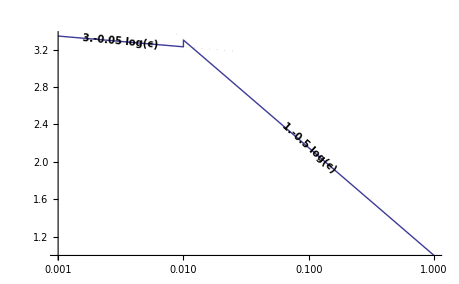

```mathematica
testdat1=Table[{x,3-.05Log[x]+RandomReal[0.0001]},{x,0.001,0.01,0.0001}]~Join~Table[{x,1-.5Log[x]+RandomReal[0.0001]},{x,0.01,1,0.01}];
fits=FindAllFits[testdat1,LogLinFitFun,10,0.25];
plt=ListLogLinearPlot[testdat1,PlotRange->{All,All},Joined->True,PlotStyle->Thick];
ratio=GetPlotCoordinateRatio[plt]; (*important to do it once (takes time)*)
Show[plt,Map[PlotFitInLog[#][[1]]&,fits],
ImageSize->CalcImgSize[1.],PlotLabel->None,
Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio, LimiterSize->Medium][[2]]&,fits]]
```

## Excess Entropy Decomposition Based on δh

The main Function is DecomposeAndPlotExcessEntropy, see below

Theoretically for a D-dim attractor with D=Floor[D] + δD
we should have
δh = - (1 - δD) log ϵ if m = Floor[D]
δh = - δD log ϵ if m = Floor[D]+1
See DecomposeAndPlotExcessEntropy2m

In the real data we find often more than 2 δh with a significant nonzero incline, so that we use a set of δh that are eps - dependent

Slice is a vertical slice though the data (see DataWithFitsAndDerivativesTagged) , so we have
{{{x, y’, dy’/dx,y}, True | False(fitted),True | False(extrapolated), prevStraight}, { ...}}
for the same x, Length[slice]=max_m
assignedMRange is one element of the output of AssignMRangeToStochasticRanges (which δH-range is  eps-dependent etc)
Output: {x,state,middle,memory,excess_raw, RulesforQualityValues}
state+middle+memory is the excess entropy (from fits). The excess entropy from raw data is in excess_raw)
MiddleFitted tells whether the components of the middle sum are fitted or not

```mathematica
Options[CalcEEDecompostion]={ConstThresh->0.01, RemoveNegative->False,UseLargerRangePlateaus->True}; 
ConstThresh::usage="Threshold under which a line is considered constant (straight) (for detection of plateaus on larger scales)";
RemoveNegative::usage="Remove negative values of δh";
UseLargerRangePlateaus::usage="Use values of deltaH's from larger range to add to memory complexity (and substract from middle)"
```

Use values of deltaH's from larger range to add to memory complexity (and substract from middle)

```mathematica
CalcEEDecompostion[slice_List,assignedMRange_,opts:OptionsPattern[CalcEEDecompostion]]:=Module[{numNoFits,containsIndeterminates,numExtrapolation,numNegative,maxM,numMDropped,sliceClean,
lowerM,upperM,determinism,isDeterministic,fromLargerRange},
containsIndeterminates=Count[slice,Indeterminate,{3}]>0;
numNoFits=Count[slice[[All,2]],False];
maxM=Length[slice];
numMDropped=Count[slice,{{_,Indeterminate,__},__}];
numNegative=Count[slice,{{x_,y_,__},__}/;y<-0.001];
numExtrapolation=Count[slice[[All,3]],True];
sliceClean=slice/.{Indeterminate->0};
sliceClean=If[OptionValue[RemoveNegative],Map[Function[{x},If[x[[1,2]]<0,ReplacePart[x,{1,2}->0],x]],sliceClean],sliceClean];
{lowerM,upperM,determinism,isDeterministic}=assignedMRange;
fromLargerRange = If[OptionValue[UseLargerRangePlateaus],Total[Table[m sliceClean[[Max[m,1],4]],{m,lowerM,upperM}]],0];
{sliceClean[[1,1,1]],
ExcessEntropySumPart[sliceClean,1,Max[0,lowerM-1]]+ fromLargerRange,
ExcessEntropySumPart[sliceClean,lowerM,upperM] - fromLargerRange,
ExcessEntropySumPart[sliceClean,upperM+1],
ExcessEntropySumPart[slice[[All,{1},{1,4}]],1,-1],
{"lowerM"->lowerM,
"upperM"->upperM,
"stochasticity"->1-determinism,
"isDeterministic"->isDeterministic,
"numMDropped"->numMDropped,
"numNoFits"->numNoFits,
"indet"->containsIndeterminates,
"extrapol"->numExtrapolation,
"negative"->numNegative,
"fromLargerRange"->fromLargerRange}
}
]
```

Replaces fitted intervals in data and adds the derivatives (either from fit of from data). Each point is tagged whether it came from an fitted interval and whether it was extrapolated. y’ is the new y from fitting. The original y is also included.
{{{x,y’,dy’/dx,y},fromInterval(True/False),extrapolated(True/False)},...}

```mathematica
Options[DataWithFitsAndDerivativesTagged]={NumPointForDerivative->5,ReplaceEndByFits->False};
ReplaceEndByFits::usage="use to extapolate data at the end by the fits, (everything after the last fit is replaced by it)";
NumPointForDerivative::usage="number of points used to calculate numerical derivative at each point (default 5)";
DataWithFitsAndDerivativesTagged[dat_,fits_,opts:OptionsPattern[DataWithFitsAndDerivativesTagged]]:=
Module[{intervals,tagged,derivatives,getIncline,posLastFit,lastFitIdx},
derivatives=LogDerivativeSeries[dat,OptionValue[NumPointForDerivative]];
intervals=fits[[All,3]];
getIncline[fit_,p_]:=(fit[p]-fit[p+0.0001])/(Log[p]-Log[p+0.0001]);
tagged=Map[Function[{idx},{idx,Flatten[Position[Map[IntervalMemberQ[#,idx]&,intervals],True]]}],Range[1,Length[dat]]];
posLastFit=Length[tagged];
If[OptionValue[ReplaceEndByFits],(* replace everything after last fit by the fit*)
posLastFit=Length[tagged]-First[DefaultMissing[FirstPosition[Reverse[tagged],{_,{_Integer}}],{1}]]+1;
lastFitIdx=tagged[[posLastFit,2]];
tagged=ReplacePart[tagged,Table[{i,2}->lastFitIdx,{i,posLastFit+1,Length[tagged]}]];
];
Map[Function[{idx,matches},
If[Length[matches]<1,
{{dat[[idx,1]],dat[[idx,2]],derivatives[[idx,2]],dat[[idx,2]]},False,False},
{{dat[[idx,1]],Mean[Map[#[dat[[idx,1]]]&,fits[[matches,1]]]],
Mean[Map[getIncline[#,dat[[idx,1]]]&,fits[[matches,1]]]],
dat[[idx,2]]},
idx≤posLastFit,idx>posLastFit}]]@@#&,tagged]
]
```

```mathematica
Options[DecomposeAndPlotExcessEntropy]={DeltaHFlatThreshold->0.05,DeterminismThreshold->0.5,YPlotRangeMax->Automatic,XTicks->Automatic,FactorForQualityScales->Automatic,
DimLabelsEvery->Automatic,MaxDimScale->Automatic,ShowRawExcessEntropy->True,
ShowMDropped->True,ShowSceptical->False,ShowQualStochastic->True,ShowNumNoFits->True,ShowNegative->False,
ShowLegend->True
}~Join~Options[CalcEEDecompostion]~Join~Options[ListLogLinearPlot]~Join~Options[DataWithFitsAndDerivativesTagged]; 
DeltaHFlatThreshold::usage="derivative under which deltaH is considered flat. (0.05)";
DeterminismThreshold::usage="if the sum of eps-dependend δH is larger than this threshold it is considered to be deterministic (0.5)";
ShowRawExcessEntropy::usage="Show also the raw excess entropy without the fits";
YPlotRangeMax::usage="maximal Y-PlotRange used also for rescaling right axis";
XTicks::usage="Explicit ticks specs for x axis";
FactorForQualityScales::usage="size of quality scales w.r.t. the dim scale (Automatic)";
MaxDimScale::usage="scale of dimension axis (for m's)";
DimLabelsEvery::usage="labeled ticks every so often in dimension scale";
ShowMDropped::usage="Show number m dropped";
ShowSceptical::usage="whether sum contains mssing data (also in MDropped)";
ShowQualStochastic::usage="Show quality of determinstic/ amount of stochasticity";
ShowNegative::usage="Show indicate whether there are negatives";
ShowNumNoFits::usage="Show number of m's where we have no fit";
ShowLegend::usage="show a legend or not";
```

```mathematica
DecomposeAndPlotExcessEntropy[dat_,fits_,opts:OptionsPattern[DecomposeAndPlotExcessEntropy]]:=Module[{datandfits,merged,straights,maxM,allderivs,mRangeDet,mergedFitsDerivStraights,decomp,
cState,cMiddle,cMem,cSM,cAll,ee,opts4plot, plt,
optsForDatReplacement,aux,lowerM,upperM,stochasticity,maxDimScale,factorQual,numNoFits,sceptical,numMDropped,detOrStoc,negative,extrapol,maxQual,datarange,plotrange,rescale,rescaleQual,mLabelsEvery,axeslabel,rightaxis,rightoffset,rescaleQualDat,QualityQuants,colors,plotstyle,legend
},
datandfits=Zip[dat,fits];
optsForDatReplacement=FilterRules[{opts},Options[DataWithFitsAndDerivativesTagged]];
merged=Map[DataWithFitsAndDerivativesTagged [#[[1]],#[[2]],optsForDatReplacement]&,datandfits];
straights=Map[GetPlateauOnLargerScaleWithoutDip[#[[1]],#[[2]],OptionValue[DeltaHFlatThreshold]]&,datandfits];
allderivs = -Transpose[merged][[All,All,1,3]]; (*all derivative (negated, because we are intersted in D of const - D log(eps)*)
(*range of m's for eps-dependent part and stochasticity, {{Subscript[m, lower]^*,Subscript[m, upper]^*,stochasticity,isDeterministic (True/False)},...}*)
mRangeDet=AssignMRangeToStochasticRanges[Map[GetEpsDepMAndDeterminism[#,OptionValue[DeltaHFlatThreshold]]&,allderivs],
OptionValue[DeterminismThreshold],10]; 
(*{curves} with curve={{{x,y,dy/dx},True|False,prevStraight},{...}}*)
mergedFitsDerivStraights=Map[Function[{m,s},Map[Append[#[[1]],#[[2]]]&,Zip[m,s]]]@@#&,Zip[merged,straights]];
decomp=SortBy[Map[CalcEEDecompostion[#[[1]],#[[2]],FilterRules[{opts},Options[CalcEEDecompostion]]]&,Zip[Transpose[mergedFitsDerivStraights],mRangeDet]],First];
cState=decomp[[All,{1,2}]];
cMiddle = decomp[[All,{1,3}]];
cMem=decomp[[All,{1,4}]];
cSM =CombineTimeSeries[Plus,cMem,cState]; (*mem + state*)
cAll=CombineTimeSeries[Plus,cSM,cMiddle]; (*plus middle term*)
ee=decomp[[All,{1,5}]]; (*raw excess entropy*)
maxM=Length[dat];
aux=decomp[[All,{1,6}]];
upperM=MapTimeSeries["upperM"/.#&,aux];
lowerM=MapTimeSeries["lowerM"/.#&,aux];
numNoFits=MapTimeSeries[("numNoFits"/.#)/maxM&,aux];
sceptical=MapTimeSeries[If["indet"/.#,1,0]&,aux];
numMDropped=MapTimeSeries[("numMDropped"/.#)/maxM&,aux];
extrapol=MapTimeSeries[("extrapol"/.#)/maxM&,aux];
stochasticity=MapTimeSeries["stochasticity"/.#&,aux];
detOrStoc=MapTimeSeries[If["isDeterministic"/.#,Missing[],1]&,aux];
(*negative=MapTimeSeries[If[("negative"/.#)>0,1,0]&,aux];*)
negative=MapTimeSeries[("negative"/.#)/maxM&,aux];
QualityQuants=Cases[
{If[OptionValue[ReplaceEndByFits],{extrapol,"% extrap.",Directive[Gray],ShowMDropped},{numMDropped,"% dropped",Directive[Gray],ShowMDropped}],
{sceptical,"sceptical",Directive[Gray],ShowSceptical},{numNoFits,"% no fits",Directive[Cyan],ShowNumNoFits},{negative,"% negative",Directive[Lighter[Red]],ShowNegative},
{stochasticity,"stochastic",Directive[Green],ShowQualStochastic}
},{_,_,_,v_}/; OptionValue[v]];
maxQual=Length[QualityQuants];
maxDimScale=If[OptionValue[MaxDimScale]===Automatic,Max[upperM[[All,2]]],OptionValue[MaxDimScale]] ;
mLabelsEvery= If[OptionValue[DimLabelsEvery]===Automatic,Ceiling[maxDimScale/2],OptionValue[DimLabelsEvery]] ;
factorQual= If[OptionValue[FactorForQualityScales]===Automatic,Ceiling[maxDimScale/5],OptionValue[FactorForQualityScales]] ;
datarange=maxDimScale +(factorQual*2) maxQual;
plotrange=If[OptionValue[YPlotRangeMax]===Automatic,Max[cAll[[All,2]]]*1.2,OptionValue[YPlotRangeMax]];
rightoffset=plotrange/2;
rescale[x_]:=(x) (plotrange-rightoffset)/datarange+rightoffset;
rescaleQual[x_,i_]:=(factorQual x+maxDimScale+factorQual.5+(factorQual*2)i-1) (plotrange-rightoffset)/datarange+rightoffset;
rescaleQualDat[data_,i_]:=MapTimeSeries[rescaleQual[#,i]&,data];
rightaxis=Table[{rescale[v],If[Mod[v,mLabelsEvery]==0,ToString[v],""]},{v,0,maxDimScale,1}]~Join~
Flatten[MapIndexed[Function[{x,i},{{rescaleQual[0,First[i]],""},{rescaleQual[1,First[i]],x[[2]]}}],QualityQuants],1];opts4plot = FilterRules[{opts},Options[ListLogLinearPlot]];
(*colors={ColorData[1,2],ColorData[1,1],ColorData[1,3],ColorData[1,4]};*)
colors={Blue,Darker[Red],Orange,ColorData[1,4]};
plotstyle=Flatten[{{colors[[1]],Directive[Dashed,colors[[2]]],colors[[3]]},
If[OptionValue[ShowRawExcessEntropy],{Directive[Darker[ColorData[1,3]]]},{}],
{Directive[colors[[4]],Dotted],Directive[colors[[4]],DotDashed]},QualityQuants[[All,3]],{None}},1];
plt=ListLogLinearPlot[Flatten[{{cMem,cSM,cAll},If[OptionValue[ShowRawExcessEntropy],{ee},{}],
{MapTimeSeries[rescale,lowerM],MapTimeSeries[rescale,upperM]},
MapIndexed[Function[{x,i},MapTimeSeries[rescaleQual[#,First[i]]&,First[x]]],QualityQuants],
{MapTimeSeries[rescaleQual[#,maxQual]&,detOrStoc]}
},
1],
opts4plot,PlotRange->{Automatic,{Automatic,rescaleQual[1,maxQual]}},FrameLabel->{None,EEm},
Prolog->Inset[Style[ϵ,12,FontFamily->"Times New Roman"],ImageScaled[{.85,.05}]],PlotRangeClipping->False,
PlotStyle->plotstyle,
Filling->Flatten[{{1->0,2->{1},3->{{2},Directive[Opacity[.3],RGBColor[1,0.9,0]]},6->{{5},Directive[Opacity[.1],colors[[3]]]}},
Table[If[OptionValue[ShowRawExcessEntropy],6,5]+i->rescaleQual[0,i],{i,1,maxQual}],
{If[OptionValue[ShowRawExcessEntropy],6,5]+maxQual+1->{0,Directive[Opacity[.05],Black]}}},
1],
Joined->True,
Frame->{{True,True},{True,False}},
FrameTicks->{{Automatic,rightaxis},{OptionValue[XTicks],None}},
FrameTicksStyle->{{Automatic,Directive[6]},{Automatic,Automatic}},
Axes->{False,False},
GridLines->{None,{rescale[0]}~Join~Table[rescaleQual[1,x],{x,1,maxQual}]},GridLinesStyle->Directive[LightGray,Dashed],PlotLegends->If[OptionValue[ShowLegend],LineLegend[Flatten[{{"memory","core\n(state+mem)","excess Ent.\ndecomp"},If[OptionValue[ShowRawExcessEntropy],{"excess Ent.\n raw"},{}],{"m_l","m_u"}},1]],None]
];
legend=LineLegend[plotstyle,Flatten[{{"memory ","core (state+mem) ","excess Ent. decomp "},If[OptionValue[ShowRawExcessEntropy],{"excess Ent. raw "},{}],{"m_l ","m_u "}},1],LegendLayout->{"Row",1}];
{plt,decomp,{"legend"->legend,"straights"->straights}}
]
```

Fits lines (in log scale) onto all δh. Returns {δh, fits, plot of δh with fits}

```mathematica
Options[FitDeltaHs]={MinFitLength->10,FitQualityQuantile->0.25,ShowFitLines->{}}~Join~Options[PlotFitInLog];
MinFitLength::usage="minimal length if fits in number of data points";
FitQualityQuantile::usage="quantile under which are considered good (w.r.t to all possible fits)";
ShowFitLines::usage="selector for fitline to plot";

FitDeltaHs[plots_,tiseandat_,opts:OptionsPattern[FitDeltaHs]]:=Module[{dat,plt,fits,ratio,opts4labels},
dat = "deltaH"/.tiseandat;
plt=plots[[5]];
fits=Map[FindAllFits[#,LogLinFitFun,OptionValue[MinFitLength],OptionValue[FitQualityQuantile]]&,dat];
If[OptionValue[ShowLabel],
ratio=GetPlotCoordinateRatio[plt];
opts4labels ={LabelAngle->Automatic,BasePlotRatio->ratio} ~Join~FilterRules[{opts},Options[PlotFitInLog]];
,	
opts4labels =FilterRules[{opts},Options[PlotFitInLog]];
];
{dat,fits,Show[plt,Map[PlotFitInLog[#][[1]]&,Flatten[fits,1][[OptionValue[ShowFitLines]]]],PlotLabel->None,Epilog->Map[PlotFitInLog[#,opts4labels][[2]]&,Flatten[fits,1]]]
}
]
```

For each point it gives the minimum of the value of the previous flat line fit and the actual data.

```mathematica
GetPlateauOnLargerScaleWithoutDip[dat_,fits_, flatThresh_:0.01]:=Module[{getFit,getIncline},
getIncline[fit_,p_]:=(fit[p]-fit[p+0.0001])/(Log[p]-Log[p+0.0001]);
getFit[x_]:=First[FirstPosition[fits[[All,2]],int_List/;IntervalMemberQ[Interval[int],x],{0},2]];
Drop[FoldList[Function[{last,x},Block[{match=getFit[x[[1]]]},
If[match==0 || -getIncline[fits[[match,1]],x[[1]]]≥flatThresh,Max[0,Min[last,x[[2]]],0],
Max[0,fits[[match,1]][x[[1]]]]]
]
],0,dat/.Indeterminate->0],1]
]
```

```mathematica
ExcessEntropySumPart[deltaHslice_,start_Integer,end_Integer:-1]:=Module[{ls,minm,maxm},
minm=Max[start,1];
maxm=Min[Length[deltaHslice],If[end< 0,Length[deltaHslice],end]];
Sum[k (deltaHslice[[k,1,2]]),{k,minm,maxm}]
]
```

```mathematica
CombineTimeSeries[fun_,s1_List,s2_List]:=Block[{f=Function[{vs1,vs2},{vs1[[1]],fun[vs1[[2]],vs2[[2]]]}]},Map[Function[{vs1,vs2},{vs1[[1]],fun[vs1[[2]],vs2[[2]]]}]@@#&,Zip[s1,s2]]];
```

```mathematica
CombineTimeSeries[Plus,{{1,1},{2,4}},{{1,4},{2,0}}]
```

{{1,5},{2,4}}

```mathematica
If[Length[FirstPosition]==0,
FirstPosition[expr_,pattern_,default_:Missing["NotFound"],levelspec_:Infinity]:= Replace[Position[expr,pattern,levelspec],{{}:> default, l_:> First[l]}]
];
```

finds the maximum derivative and returns the indices of the lowest and largest derivative around it that it at least flatThreshold together with the sum of the derivative within this block. Input: derivatives of deltaH curves for m=1...
Output: {lower_m,upper_m, sum from lower_m to upper_m}

```mathematica
GetEpsDepMAndDeterminism[derivatives_,flatThreshold_]:=Module[{maxd,posmaxd,below,above,lowerM,upperM,sum},
{maxd,posmaxd}=MaxWithPosition[derivatives];
below=Reverse[derivatives[[1;;posmaxd-1]]];
above=derivatives[[posmaxd+1;;]];
lowerM=posmaxd-(First[FirstPosition[below,x_/;x<flatThreshold,{Length[below]+1}]]-1);
upperM=posmaxd+(First[FirstPosition[above,x_/;x<flatThreshold,{Length[above]+1}]]-1);
{lowerM,upperM,Total[derivatives[[lowerM;;upperM]]]}
]
```

```mathematica
{GetEpsDepMAndDeterminism[{0,1,0,0},0.1]=={2,2,1},
GetEpsDepMAndDeterminism[{0,0,0,1},0.1]=={4,4,1},
GetEpsDepMAndDeterminism[{0,0.1,0.2,0},0.1]=={2,3,0.3},
GetEpsDepMAndDeterminism[{0.4,0.6,0,0},0.1]=={1,2,1},
GetEpsDepMAndDeterminism[{0.2,0.4,0.2,0.2},0.1]=={1,4,1}}
```

{True,True,True,True,True}

For stochastic scaling range we use m_lower and m_upper from previous deterministic range
Input: {{m_lower,m_upper,stochasticity},...} for all eps (from large eps to small eps!), see GetEpsDepMAndDeterminism
Output {{m_lower^*,m_upper^*,stochasticity, isDeterministic (True/False)},...} where the m^* are the replaced ones if the stochasticity > detThreshold.
To determine correct m’s from previous range a averaging is performed.

```mathematica
MovingAverageHalf[list_,r_]:=Map[Mean,Partition[list,r,1,{-1,-1},0]]
AssignMRangeToStochasticRanges[mRangeAndStochasticity_,detThreshold_,averaging_]:=Module[{mrangeWithAvgs},
mrangeWithAvgs=Zip[mRangeAndStochasticity,Zip[MovingAverageHalf[mRangeAndStochasticity[[All,1]],averaging],MovingAverageHalf[mRangeAndStochasticity[[All,2]],averaging]]];
Drop[FoldList[Function[{acc,ms},Block[{lastrange=acc[[1]]},
If[ms[[1,3]]<detThreshold,{lastrange,lastrange~Join~{ms[[1,3]],False}},
{Round[ms[[2]]],Append[ms[[1]],True]}
]]],{{0,0},{}},mrangeWithAvgs]
,1][[All,2]]
]
```

Returns the mean and stddev of the state and core complexity in the given interval

```mathematica
GetAvgDecomp[eeDecomp_List,int_Interval]:=Module[{relevant},
relevant=Select[eeDecomp,IntervalMemberQ[int,#[[1]]]&];
{"state"->PlusMinus[Mean[relevant[[All,2]]] ,StandardDeviation[relevant[[All,2]]]],
"memory"->PlusMinus[Mean[relevant[[All,4]]], StandardDeviation[relevant[[All,4]]]],
"state+memory"->PlusMinus[Mean[relevant[[All,2]]]+Mean[relevant[[All,4]]], StandardDeviation[relevant[[All,2]]]+ StandardDeviation[relevant[[All,4]]]]
}
]
```

```mathematica
Options[AvgDecompInPlot]={LabelSize->8};
AvgDecompInPlot[decomp_,int_Interval,posstate_:-1,posmem_:-1,opts:OptionsPattern[AvgDecompInPlot]]:=Module[{mi,ma,lpos,state,memory,statemem,max},
mi=Min[int];
ma=Max[int];
lpos=Exp[Mean[Log[int[[1]]]]];
state="state"/.decomp;
memory="memory"/.decomp;
statemem="state+memory"/.decomp;
max=statemem[[1]]+3(statemem[[2]]);
{{Darker[Gray],Line[{{Log[mi],0},{Log[mi],max}}],Line[{{Log[ma],0},{Log[ma],max}}]},
If[memory[[1]]>0,Inset[StyleLabel[RoundNumbersInExp[memory,0.01],OptionValue[LabelSize]],{Log[lpos],memory[[1]]-2posmem*memory[[2]]},{0,posmem}],{}],
If[state[[1]]>0,Inset[StyleLabel[RoundNumbersInExp[state,0.01],OptionValue[LabelSize]],{Log[lpos],statemem[[1]]-2posstate*statemem[[2]]},{0,posstate}],{}]
}
]
```

## Usecases

```mathematica
plots=TiseanPlotAllMultiDim["tisean/coupledtentmap/col-uni_a2p20p2_s0-05_5M_d1.d2",1,PlotRange->{All,All}];
```

```mathematica
dat = "deltaH"/.TiseanData;plt=plots[[7]];
fits=Map[FindAllFits[#,LogLinFitFun,10,0.25]&,dat];
ratio=GetPlotCoordinateRatio[plt]; 
Map[Length,fits]
Show[plt,Map[PlotFitInLog[#][[1]]&,Flatten[fits,1]],
ImageSize->CalcImgSize[1.3],PlotLabel->None,
Epilog->Map[PlotFitInLog[#,LabelAngle->Automatic,BasePlotRatio->ratio][[2]]&,Flatten[fits,1][[1;;9]]]]
```

```mathematica
DecomposeAndPlotExcessEntropy[dat,fits,0.02][[1]]
```

## Functions to plot data from KSG algorithm MIXnYn

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
EtaScale::usage="Factor for eta";
Options[PlotMIScan]={EtaScale->1/2}~Join~Options[ListLogLinearPlot];
```

```mathematica
PlotMIScan[d_,title_String,opts:OptionsPattern[PlotMIScan]]:=Module[{len,dataraw,data,pl,error,ep,opts4plot},
dataraw=GatherBy[d,First][[All,All,{3,4,5}]];
data=Map[MapAt[OptionValue[EtaScale]#&,#,1]&,dataraw,{2}];
len = Length [data];
opts4plot= FilterRules[{opts},Options[ListLogLinearPlot]];
pl=ListLogLinearPlot[Map[Sort,data[[All,All,{1,2}]]],opts4plot,Joined->True,PlotStyle->ColorsFromScheme[len,"Rainbow"],PlotTheme->None,PlotLabel->ToString[len] <> ":..." <>StringTake[title,-Min[30,StringLength[title]]],ImageSize->350,PlotRange->{Automatic,{0,All}},AxesLabel->{StyleAxisLabel[OptionValue[EtaScale]η],PIm}];
error = Map[{{Log[#[[1]]],#[[2]]},ErrorBar[{#[[3]]-#[[2]],0}]}&,data,{2}];
ep=ErrorListPlot[error,PlotStyle->ColorsFromScheme[len,"Rainbow"],PlotTheme->None];
Show[pl,ep]
]
```